## Normal Forms BSA, 2024

```mathematica
ClearAll["Global`*"]
```

### Input

```mathematica
A  = {{0, 1, 0, a}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}};
B  = A - λ * IdentityMatrix[4];
A0 = A /. a -> 0;
A1 = A /. a -> 1;
```

```mathematica
Print["A = ", MatrixForm[A], ", A0 = ", MatrixForm[A0], ", A1 = ", MatrixForm[A1]]
```

A = (0 | 1 | 0 | a
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0), A0 = (0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0), A1 = (0 | 1 | 0 | 1
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
Print["B = ", MatrixForm[B]]
```

B = (-λ | 1 | 0 | a
-1 | -λ | 0 | 0
0 | 0 | -λ | 1
0 | 0 | -1 | -λ)

### Jordan form

```mathematica
J0 = JordanDecomposition[A0][[2]];
J1 = JordanDecomposition[A1][[2]];
```

```mathematica
Print["J0 = ", MatrixForm[J0], ", J1 = ", MatrixForm[J1]]
```

J0 = (-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ), J1 = (-ⅈ | 1 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 1
0 | 0 | 0 | ⅈ)

### Stability condition

```mathematica
StabilityCondition[M_] := Module[{S, J}, {S, J} = JordanDecomposition[M];
	Length[Cases[Table[If[Re[J[[i, i]]] < 0 || (Re[J[[i, i]]] == 0 && Re[J[[i, i + 1]]] == 0), 1, 0], {i, 1, Length[J] - 1}], x_ /; x == 0]] == 0 && 
	Re[J[[-1, -1]]] <= 0
];
CheckStability[M_] := If[StabilityCondition[M], Print["Stable"], Print["Unstable"]];
```

```mathematica
CheckStability[A0]
```

Stable

```mathematica
CheckStability[A1]
```

Unstable

### Smith canonical form

```mathematica
DD[n_, M_] := PolynomialGCD @@ Flatten[Minors[M, n]];
F[n_, M_]  := Factor[Expand[DD[n, M] / DD[n - 1, M]]];
S0 = DiagonalMatrix[Table[F[k, B /. a -> 0], {k, 4, 1, -1}]];
S1 = DiagonalMatrix[Table[F[k, B /. a -> 1], {k, 4, 1, -1}]];
```

```mathematica
Print["S0 = ", MatrixForm[S0], ", S1 = ", MatrixForm[S1]]
```

S0 = (1+λ^2 | 0 | 0 | 0
0 | 1+λ^2 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1), S1 = ((1+λ^2)^2 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

### Compute the solution

```mathematica
X = {x1[t], x2[t], x3[t], x4[t]};
InX = {x1[0] == 1, x2[0] == 1, x3[0] == 1, x4[0] == 1};
Eq0 = Thread[D[X, t] == A0.X];
Eq1 = Thread[D[X, t] == A1.X];
Sol0 = X /. DSolve[Union[Eq0, InX], X, t][[1]];
Sol1 = X /. DSolve[Union[Eq1, InX], X, t][[1]];
```

```mathematica
Print["X0 = ", MatrixForm[Sol0], ", X1 = ", MatrixForm[Sol1]]
```

X0 = (Cos[t]+Sin[t]
Cos[t]-Sin[t]
Cos[t]+Sin[t]
Cos[t]-Sin[t]), X1 = (1/2 (2 Cos[t]+t Cos[t]+3 Sin[t]-t Sin[t])
1/2 (2 Cos[t]-t Cos[t]-Sin[t]-t Sin[t])
Cos[t]+Sin[t]
Cos[t]-Sin[t])

### Plot the solution

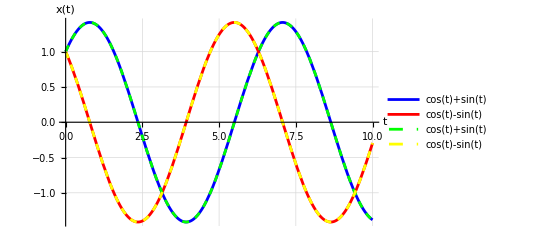

```mathematica
Plot[Sol0, {t, 0, 10}, PlotLegends -> Placed["Expressions", Right], AxesLabel -> {t, x[t]}, 
	GridLines -> Automatic, PlotStyle -> {Blue, Red, {Green, Dashed}, {Yellow, Dashed}}, PlotRange -> All]
```

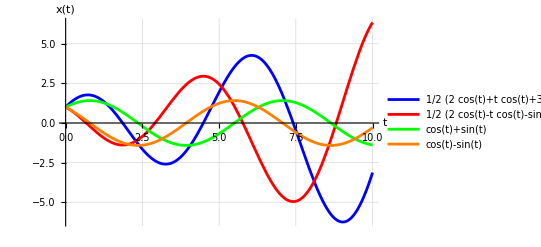

```mathematica
Plot[Sol1, {t, 0, 10}, PlotLegends -> Placed["Expressions", Right], AxesLabel -> {t, x[t]}, 
	GridLines -> Automatic, PlotStyle -> {Blue, Red, Green, Orange}, PlotRange -> All]
```